## Bayesian regression

Following the setup in Section 3.3.1 (Bayesian Linear Regression) of Bishop (2007).
Created: March 30 2016, John Aslanides.

## Setup

```mathematica
α=2; (*prior hyperparameter*)
β=5; (*noise hyperparameter*)
n=20; (*size of sample*)

Subscript[w, truth]={-0.3,0.5,0.9,0.2}; (*parameters of generative process*)
ϕ[x_]:=Flatten@{1,x} (*add bias feature*)
d=Length@Subscript[w, truth]; (*dimensionality of the feature space*)
basis=Table[x^i,{i,d-1}]; (*use polynomial basis functions*)

params=Table[Subscript[w, i],{i,d}]; (*vector of dummy variables*)
f[x_,w_List] :=NormalDistribution[w.ϕ[x],β^-1] (*generative model*)

data=Map[{#,RandomVariate@f[#,Subscript[w, truth]]}&,RandomVariate[UniformDistribution[Table[{-1,1},{d-1}]],n]]; (*generate a bunch of data (in [-1,1])^(d-1) × ℝ*)
```

## Brute-force solution (numerical integration)

```mathematica
prior = PDF[MultinormalDistribution[Table[0,{d}],α^-1 IdentityMatrix[d]],params];
likelihood[d_,w_List] := PDF[f[d⟦1⟧,w],d⟦2⟧]
normalization[d_,pr_]:=ComplexExpand@Re@Integrate@@Flatten[{likelihood[d,params]pr,{#,-∞,∞}&/@params},1]
posterior[pr_,d_]:=(likelihood[d,params] pr)/normalization[d,pr]
(*posts=FoldList[posterior,prior,data]*) (*warning: very slow*)
```

## Closed-form solution

```mathematica
Φ=ϕ[#⟦1⟧]&/@data; (*construct design matrix*)
y=#⟦2⟧&/@data; (*construct vector of targets*)
S[Φ_]:=Inverse[α IdentityMatrix[d]+ β Φᵀ.Φ] (*closed form of variance of posterior*)
m[Φ_,t_]:=β S[Φ].Φᵀ.t; (*closed form of mean of posterior*)
Ss=Prepend[Table[S[Φ⟦1;;i⟧],{i,n}],α IdentityMatrix@d]; (*compute for each data point*)
ms = Prepend[Table[m[Φ⟦1;;i⟧,y⟦1;;i⟧],{i,n}],Table[0,{d}]];
```

## Plots

```mathematica
(*tools for plotting 2D projections of multidimensional distributions*)
cplot[f_,i_:1,j_:2]:=Show[ContourPlot[f,{Subscript[w, i],-1,1},{Subscript[w, j],-1,1},PlotRange-> Full,ColorFunction->"DarkRainbow",FrameLabel->{{Style[Subscript[w, i],Bold],None},{Style[Subscript[w, j],Bold],None}}],ListPlot[{Subscript[w, truth]⟦{i,j}⟧},PlotMarkers->Style["X",White]],ImageSize-> 500]
ccplot[i_,j_]:=MapThread[cplot[PDF[MultinormalDistribution[#1,#2],params]/.Table[Subscript[w, n]->#1⟦n⟧,{n,Complement[Table[m,{m,d}],{i,j}]}],i,j]&,{ms,Ss}]
```

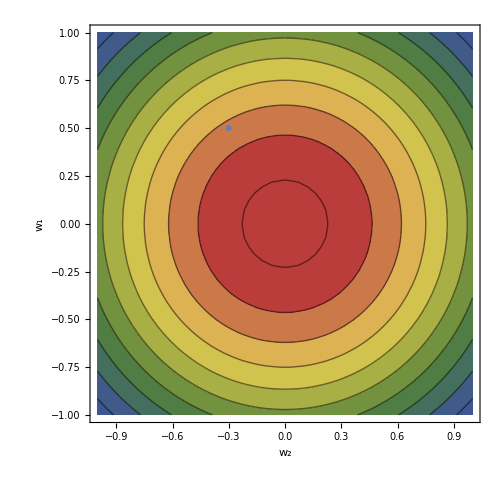
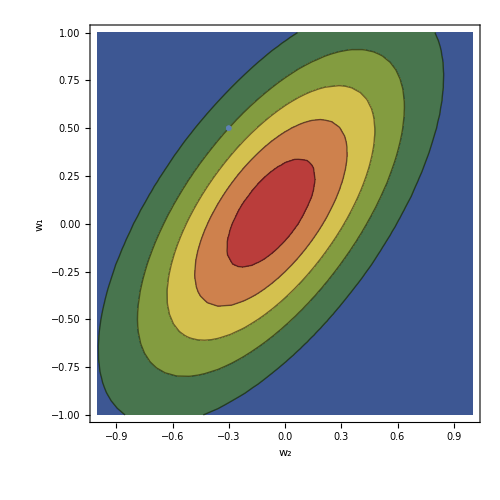
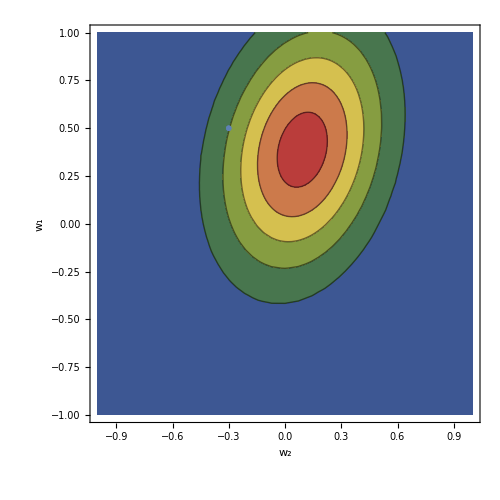
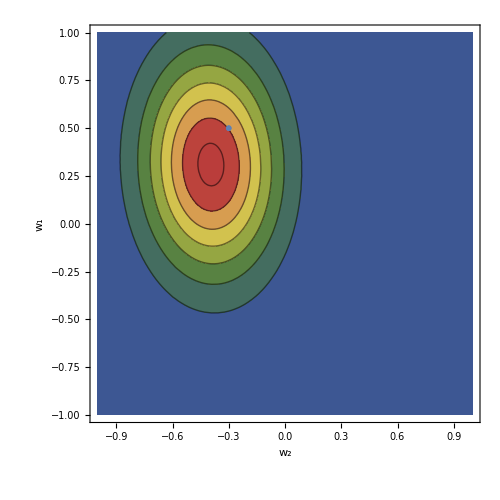
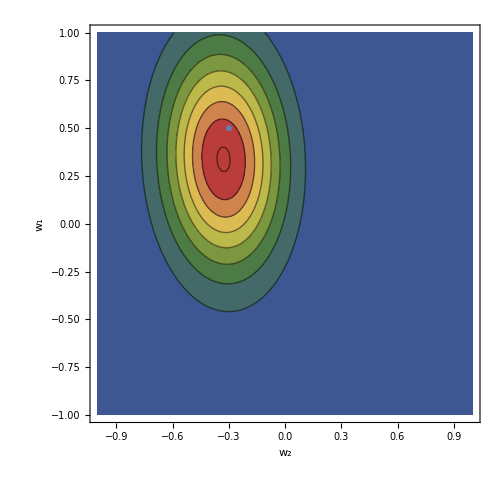
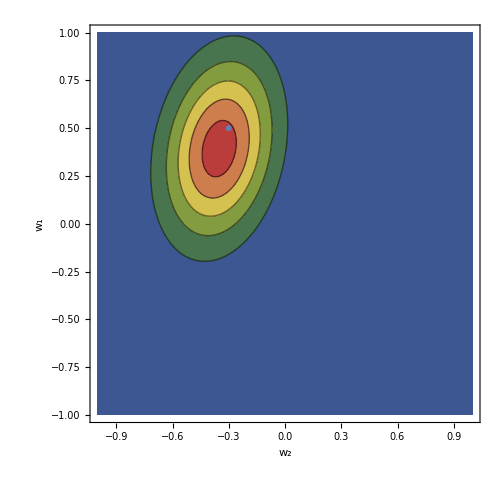
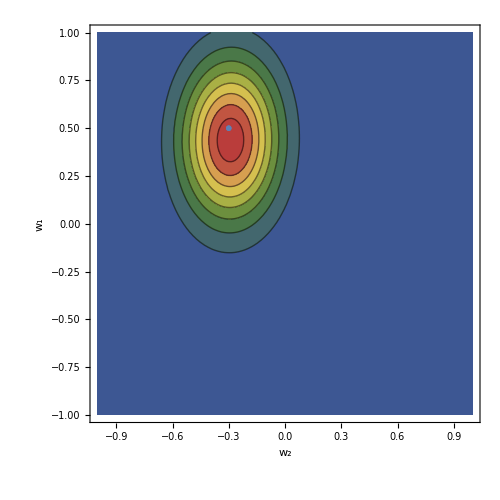
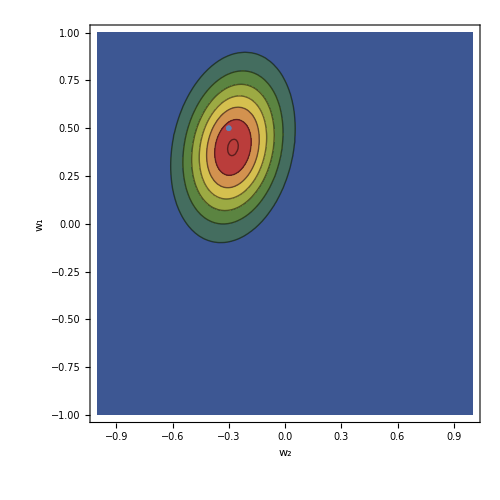

```mathematica
SetDirectory@NotebookDirectory[];
plts=ccplot[1,2]
Do[Export["../figures/plt"<>ToString@i<>".png",plts⟦i⟧],{i,Length@plts}]
```

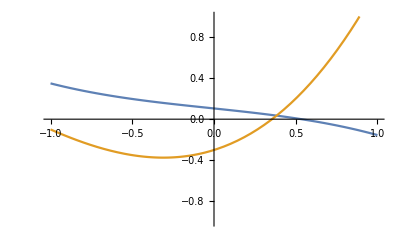
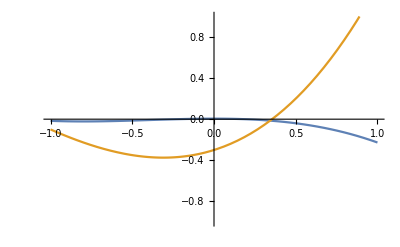
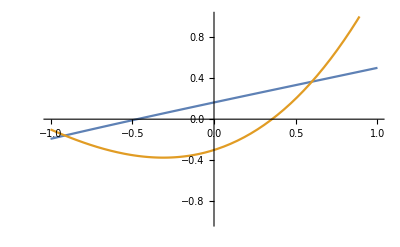
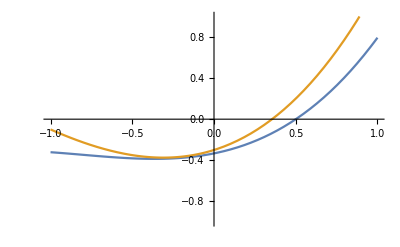
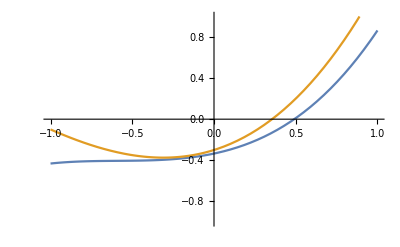
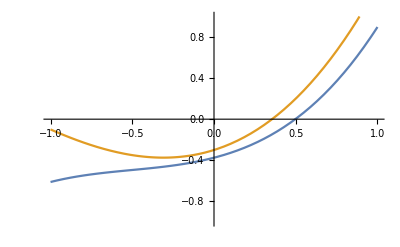
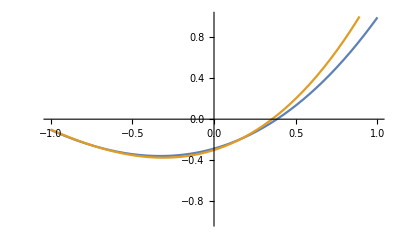
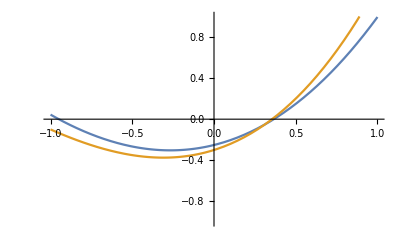

```mathematica
models=ϕ[basis].#&/@(Mean@RandomVariate[#,100]&/@MapThread[MultinormalDistribution[#1,#2]&,{ms,Ss}]);
Plot[{#,ϕ[basis].Subscript[w, truth]},{x,-1,1},PlotRange-> {{-1,1},{-1,1}}]&/@models
```